```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Пламя/Пламя.xlsx,/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Пламя/~$Пламя.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/Кафедра квантовой радиофизики/5 семестр/Пламя/Пламя.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 1

```mathematica
dataset1 = makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs = dataset1[All, <|"I"-> (Around[#I,#dI] &), "T" -> (Around[#T,#dT] &)|>]
```

Dataset[<>]

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

```mathematica
datasetline =raw⟦2⟧⟦2;;⟧⟦All,{1,3}⟧
```

{{2.15,2275.},{2.,2178.},{1.9,2088.},{1.8,1988.},{1.75,1923.},{1.7,1873.},{1.75,1823.},{1.625,1773.},{1.5,1673.},{2.025,2153.},{1.95,2033.}}

```mathematica
line1 = LinearModelFit[datasetline,{1,x},x]
```

FittedModel[246.494+946.331 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 246.494 | 126.339 | 1.95105 | 0.0828273
x | 946.331 | 68.6261 | 13.7897 | 2.33722×10^-7

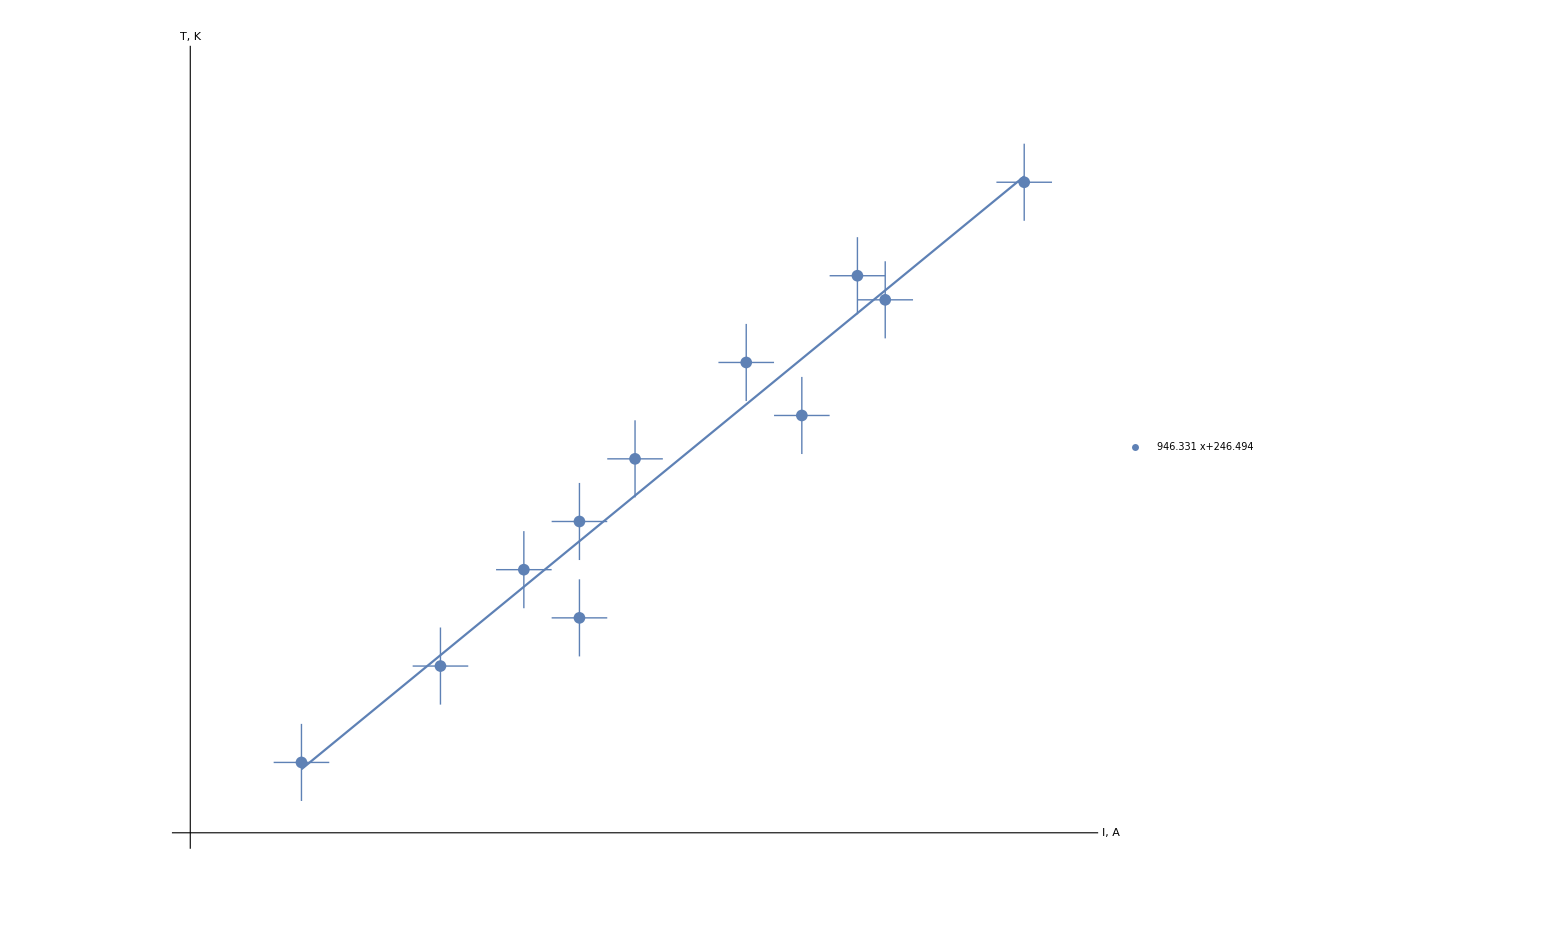

```mathematica
Show[
ListPlot[
{dataset1WithErrs},
PlotRange-> {{1.4,2.2},{1600,2400}},
Ticks-> {Range[-1000,1000, 0.05],Range[-10000,10000, 100]},
TicksStyle->Directive[Black, 14],
PlotMarkers-> {Automatic, 12},
AxesLabel-> {Style["I, A", Large], Style["T, K", Large]},
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
GridLines-> {Range[-1000,1000, 0.01],Range[-10000,10000, 10]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
{Normal@line1},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.3],Scaled[0.75]}
]
],
Plot[line1[x],{x,1.5,2.150}]
]
```

## Температура пламени

T = 1970 ± 250 К